# Virtual CPU

Let’s introduce ourselves into the realm of modern computing by first understanding how our machines work by building the simplest case of a general purpose computer. Modern hardware is base on the Von-Neumann architecture, that is, a machine that has the following components:

The ALU is the part of the machine that handles arithmetical operations like addition and substracting. The result of the operation are often sent to the registers, which behaves as variables where the user can store values and the machine can store the instruction to be executed. The instruction is then executed by the control unit and the results of the instruction can be stored in a register or the RAM. The RAM is basically an array of binary digits that will store a program or values derived from its execution.

Modern computers combine this architecture with buses that allows the user to interact with different components.

For our purposes, lets begin by building the simplest Von-Neumann machine. It will be an 10-bit computer with two arithmetic registers, A and B, one Instruction Register that will hold the instruction to be executed, an Address Register that will point to the current position in the RAM. Since our hardware will be an 10-bit machine, we will be limited to having a RAM with a total of 1024 bytes (1 Kb). Modern hardware also usually include a special type of register called the Stack Register, that will enable us to jump to other parts of a program while also remembering the position from where the jump ocurred. After the ALU performs an arithmetic operation, it needs to inform the rest of the hardware if the resulting number is positive, negative, odd, zero, etc. This will be handled by giving the ALU its own register where it will store flags which indicate the state of the resulting number.
From this description we can sketch the following architecture for our computer:

In order to visualize the results of a computation our design will also include two buffers, a textBuffer to show numeric values and a imageBuffer where a image can be drawn.

## Opcodes

In our model of a Von-Neumann computer, programs consists in a sequence of instructions that will be executed one step at a time. Instructions tell the control unit how to change the values stored in the registers or the RAM. Modern hardware like the x86-x64 processor you are using right now contain hundreds of different instructions. While is not neccesary to have a large amount of instructions in order to perform a general computation, these have been added over the passage of time in order to push further the execution speed of programs. This in turn has made learning and writing programs in x86 assembly code a daunting task.

To overcome this complexity let us define the simplest set* of instructions that we can implement on our virtual CPU. 
(*Note: By simplest set I mean a simple and understandable set of instructions. One could design an even smaller set of instructions like the ones in the esoteric programming language Brainfuck, but at the cost of making the instructions less intuitive and understandable).

Let’s sketch the behaviour of our simple instruction set. Each instruction will be followed by an argument that can represent a numeric value or memory address.

LoadA address, loads the content of RAM at address to the A register.
LoadB address, loads the content of RAM at address to the B register.
SetA value, sets register A with value.
SetB value, sets register B with value.
Store address, stores the value of register A to the memory location address.
Add, adds the value of register A to the value of register B and store it in register A.
Substract, substracts the value of register A to the value of register B and store it in register A.
Increment, increments by one unit the value of register A.
Decrement, decrement by one unit the value of register A.
Jump address, sets addressRegister to the value of address.
JumpPos address, sets addressRegister to the value of address if the register ALUFlagPositive has value of 1.
JumpNeg address, sets addressRegister to the value of address if the register ALUFlagNegative has value of 1.
JumpZero address, sets addressRegister to the value of address if the register ALUFlagZero has value of 1.
JumpNotZero address, sets addressRegister to the value of address if the register ALUFlagNotZero has value of 1.
JumpOdd address, sets addressRegister to the value of address if the register ALUFlagParity has value of 1.
Call address, stores current addressRegister value on the stack and  jump to address.
Return, sets addressRegister to the last value of the stack. If the stack is empty, halt the machine.
Print address, prints the value of RAM at address in the output buffer.
Draw address, draw a pixel in the row stored in register A, the column in register B with color from address.
Halt stops the computation.

The machine will not actually read the textual instruction, instead each instruction is assigned to a corresponding binary value. We will make the distinction between the name of the instruction and its binary value by calling the textual name of the instruction a Mnemonic and the actual binary value the OpCode.

To pair each mnemonic to a binary value we will first create a List with the names of all the instructions,

```mathematica
cpuMnemonics = {
"LoadA","LoadB","SetA","SetB","Store","Add",
"Substract","Increment","Decrement","Jump","JumpPos","JumpNeg","JumpZero","JumpNotZero","JumpOdd",
"Call","Return","Print","Draw"
};
```

and then we generate a List with all posible combinations of 8 binary digits. We can then assign the mnemonics (not neccesarily in any particular order) to the generated digits.

```mathematica
opcodes = Thread[cpuMnemonics->Take[Tuples[{0,1},10],Length[cpuMnemonics]]];
```

```mathematica
Column[opcodes]
```

LoadA→{0,0,0,0,0,0,0,0,0,0}
LoadB→{0,0,0,0,0,0,0,0,0,1}
SetA→{0,0,0,0,0,0,0,0,1,0}
SetB→{0,0,0,0,0,0,0,0,1,1}
Store→{0,0,0,0,0,0,0,1,0,0}
Add→{0,0,0,0,0,0,0,1,0,1}
Substract→{0,0,0,0,0,0,0,1,1,0}
Increment→{0,0,0,0,0,0,0,1,1,1}
Decrement→{0,0,0,0,0,0,1,0,0,0}
Jump→{0,0,0,0,0,0,1,0,0,1}
JumpPos→{0,0,0,0,0,0,1,0,1,0}
JumpNeg→{0,0,0,0,0,0,1,0,1,1}
JumpZero→{0,0,0,0,0,0,1,1,0,0}
JumpNotZero→{0,0,0,0,0,0,1,1,0,1}
JumpOdd→{0,0,0,0,0,0,1,1,1,0}
Call→{0,0,0,0,0,0,1,1,1,1}
Return→{0,0,0,0,0,1,0,0,0,0}
Print→{0,0,0,0,0,1,0,0,0,1}
Draw→{0,0,0,0,0,1,0,0,1,0}

Lastly, we can define a function that returns the opcode for each mnemonic:
OpCode[mnemonic] returns the opcode associated with mnemonic.

```mathematica
revOpcodes = Map[Reverse,opcodes];
OpCode[mnemonic_]:=ReplaceAll[mnemonic,opcodes];
```

```mathematica
OpCode["Add"]
```

{0,0,0,0,0,0,0,1,0,1}

Our programs will then consist in blocks of 2 bytes, where the first one is the opcode of the instruction, and the second one is the argument. In the case of zero argument opcodes like Increment, Decrement, Return, and Halt the convention will be that the argument is a 10-bit number with value 0, that is {0,0,0,0,0,0,0,0,0,0}.

## Screen

Our virtual hardware will also include a screen where pixels can be written with the Draw instruction. For simplicity we will use a monochrome screen with two possible colors, white and black. A call to Draw with value 0 will render a white pixel, while a call to Draw with value 1 will render a black pixel. Our screen will have a resolution of 17x17 pixels.

```mathematica
colorPalette = {White, Black};
```

## CPU

We can begin our implementation by first creating a function that will initialize the registers, RAM and buffers.

```mathematica
InitializeCPU[]:=Block[{},
halted = False;
ARegister = {0,0,0,0,0,0,0,0,0,0};
BRegister = {0,0,0,0,0,0,0,0,0,0};

addressRegister = {0,0,0,0,0,0,0,0,0,0};
instructionRegister = {0,0,0,0,0,0,0,0,0,0};
parameterRegister = {0,0,0,0,0,0,0,0,0,0};
stackPointerRegister = {0,0,0,0,0,0,0,0,0,0};

ALUPositiveFlag = 0;
ALUNegativeFlag = 0;
ALUZeroFlag = 0;
ALUNotZeroFlag = 0;
ALUParityFlag = 0;

RAM = ConstantArray[{0,0,0,0,0,0,0,0,0,0},1024];
stack = ConstantArray[{0,0,0,0,0,0,0,0,0,0},8];

textBuffer = {};
imageBuffer = ConstantArray[White,{17,17}];
];
InitializeCPU[];
```

Then we can define functions to implement each instruction. Here is a sketch of how each function is intended to behave:

The arithmetic and logical unit has the following flags
ALUPositiveFlag
ALUNegativeFlag
ALUZeroFlag
ALUNotZeroFlag
ALUParityFlag
that can be used as arguments of JumpConditional.

UpdateParity[] update the parity flag. 
UpdateALU[numericResult] updates the flags ALUPositiveFlag, ALUNegativeFlag, ALUZeroFlag, and ALUNotZeroFlag according to the base 10 number numericResult.
LoadA[address] loads the content of RAM at address to the A register.
LoadB[address] loads the content of RAM at address to the B register.
SetA[value] set register A with value.
SetB[value] set register B with value.
Store[address] store the value of register A to the memory location address.
Add[] add the value of register A to the value of register B and store it in register A.
Substract[]  substract the value of register A to the value of register B and store it in register A.
UIncrement[] increment in one unit the value of register A.
UDecrement[] decrement in one unit the value of register A.
Jump[address] set addressRegister to the value of address.
JumpConditional[address, condition] set addressRegister to the value of address if the register at condition has value of 1.
Call[address] store current addressRegister value on the stack and  jump to address.
ReturnC[] set addressRegister to the last value of the stack. If the stack is empty, halt the machine.
PrintA[address] print the value of RAM at address in the output buffer.
Draw[address], draw a pixel in the row stored in register A, the column in register B with color from address.
ResetCPU[] reset registers, flags and RAM to zero.
AddressAdvance[] increase addressRegister by one unit.
CPU[] perform one CPU cycle.

### Auxiliary

We begin with auxiliary functions like decimal-binary conversion operations and a special helper function called AddressAdvance[] that will be called on instructions that advance the Address Register to the next position. Since we have defined that each instruction is accompanied by an argument, the Address Register makes steps of two bytes.

```mathematica
BinaryNot[0]=1;
BinaryNot[1]=0;
BinaryIncrement[l_,n_ :1]:=DecimalToBinary[BinaryToDecimal[l]+n,Length[l]];
BinaryDecrement[l_, n_ :1]:=DecimalToBinary[BinaryToDecimal[l]-n,Length[l]];
DecimalToBinary[n_,size_ :10]:=PadLeft[IntegerDigits[n,2],size];
BinaryToDecimal[l_]:=FromDigits[l,2];
AddressAdvance[]:=(addressRegister = BinaryIncrement[addressRegister,2]);
```

### ALU Arithmetic operations

```mathematica
UpdateParity[]:=If[EvenQ[BinaryToDecimal[ARegister]],ALUParityFlag = 1, ALUParityFlag = 0];
UpdateALU[]:=Block[{n},
n = BinaryToDecimal[ARegister];
If[n > 0,ALUPositiveFlag = 1,ALUPositiveFlag = 0];
If[n < 0,ALUNegativeFlag = 1,ALUNegativeFlag = 0];
If[n == 0,ALUZeroFlag = 1,ALUZeroFlag = 0];
If[n != 0,ALUNotZeroFlag = 1,ALUNotZeroFlag = 0];
];
UpdateALU[numericResult_]:=Block[{},
If[numericResult > 0,ALUPositiveFlag = 1,ALUPositiveFlag = 0];
If[numericResult < 0,ALUNegativeFlag = 1,ALUNegativeFlag = 0];
If[numericResult == 0,ALUZeroFlag = 1,ALUZeroFlag = 0];
If[numericResult != 0,ALUNotZeroFlag = 1,ALUNotZeroFlag = 0];
];
Add[]:=Block[{numericResult},
numericResult = BinaryToDecimal[ARegister]+BinaryToDecimal[BRegister];
ARegister = DecimalToBinary[numericResult];
UpdateALU[numericResult];
UpdateParity[];
AddressAdvance[];
];
Substract[]:=Block[{numericResult},
numericResult = BinaryToDecimal[ARegister]-BinaryToDecimal[BRegister];
ARegister = DecimalToBinary[numericResult];
UpdateALU[numericResult];
UpdateParity[];
AddressAdvance[];
];
UIncrement[]:=Block[{numericResult},
numericResult = BinaryToDecimal[ARegister]+1;
ARegister = DecimalToBinary[numericResult];
UpdateALU[numericResult];
UpdateParity[];
AddressAdvance[];
];
UDecrement[]:=Block[{numericResult},
numericResult = BinaryToDecimal[ARegister]-1;
ARegister = DecimalToBinary[numericResult];
UpdateALU[numericResult];
UpdateParity[];
AddressAdvance[];
];
```

### Register and RAM Manipulation

```mathematica
LoadA[address_]:=Block[{},
ARegister = RAM[[BinaryToDecimal[address]+1]];
UpdateParity[];
UpdateALU[];
AddressAdvance[];
];
LoadB[address_]:=Block[{},
BRegister = RAM[[BinaryToDecimal[address]+1]];
UpdateParity[];
AddressAdvance[];
];
SetA[value_]:=Block[{},
ARegister = value;
UpdateALU[];
AddressAdvance[];
];
SetB[value_]:=Block[{},
BRegister = value;
AddressAdvance[];
];
Store[address_]:=Block[{},
RAM[[BinaryToDecimal[address]+1]] = ARegister;
AddressAdvance[];
];
```

### Flow control

```mathematica
Jump[address_]:=(addressRegister = address);
JumpConditional[address_,condition_]:=If[condition==1,
addressRegister = address;
,
AddressAdvance[];
];

Call[address_]:=Block[{stackAddress},
stackAddress = BinaryToDecimal[stackPointerRegister]+1;
stack[[stackAddress]]= addressRegister;
stackPointerRegister = BinaryIncrement[stackPointerRegister];
addressRegister = address;
];
ReturnC[]:=Block[{stackAddress},
If[BinaryToDecimal[stackPointerRegister]≠0,
stackPointerRegister = BinaryDecrement[stackPointerRegister];
stackAddress = BinaryToDecimal[stackPointerRegister]+1;
addressRegister = stack[[stackAddress]];
stack[[stackAddress]] = {0,0,0,0,0,0,0,0,0,0};
AddressAdvance[];
,
halted = True;
];
];
```

### Device communication

```mathematica
PrintA[address_]:=Block[{},
AppendTo[textBuffer,BinaryToDecimal[Part[RAM,BinaryToDecimal[address]+1]]];
AddressAdvance[];
];
Draw[address_]:=Block[{row, col, colorIndex},
row = BinaryToDecimal[ARegister];
col = BinaryToDecimal[BRegister];
colorIndex = BinaryToDecimal[Part[RAM,BinaryToDecimal[address]+1]];

imageBuffer[[row+1]][[col+1]] = colorPalette[[colorIndex+1]];
AddressAdvance[];
];
```

### Complete CPU

```mathematica
CPU[]:=Block[{},
If[!halted,
instructionRegister = Part[RAM,BinaryToDecimal[addressRegister]+1];
parameterRegister = Part[RAM,BinaryToDecimal[addressRegister]+2];

If[instructionRegister == OpCode["LoadA"], LoadA[parameterRegister]];
If[instructionRegister == OpCode["LoadB"],LoadB[parameterRegister]];
If[instructionRegister == OpCode["SetA"], SetA[parameterRegister]];
If[instructionRegister == OpCode["SetB"], SetB[parameterRegister]];
If[instructionRegister == OpCode["Store"], Store[parameterRegister]];
If[instructionRegister == OpCode["Add"], Add[]];
If[instructionRegister == OpCode["Substract"], Substract[]];
If[instructionRegister == OpCode["Increment"], UIncrement[]];
If[instructionRegister == OpCode["Decrement"], UDecrement[]];
If[instructionRegister == OpCode["Print"],PrintA[parameterRegister]];
If[instructionRegister == OpCode["Draw"],Draw[parameterRegister]];

If[instructionRegister == OpCode["Jump"], Jump[parameterRegister]];
If[instructionRegister == OpCode["JumpPos"], JumpConditional[parameterRegister,ALUPositiveFlag]];
If[instructionRegister == OpCode["JumpNeg"], JumpConditional[parameterRegister,ALUNegativeFlag]];
If[instructionRegister == OpCode["JumpZero"], JumpConditional[parameterRegister,ALUZeroFlag]];
If[instructionRegister == OpCode["JumpNotZero"], JumpConditional[parameterRegister,ALUNotZeroFlag]];
If[instructionRegister == OpCode["JumpOdd"], JumpConditional[parameterRegister,BinaryNot[ALUParityFlag]]];
If[instructionRegister == OpCode["Call"],Call[parameterRegister]];
If[instructionRegister == OpCode["Return"],ReturnC[]];
]
];
```

## Load program to memory

LoadProgram[program] load program to RAM.
ClearProgram[] clear RAM and fill it with zero values.

```mathematica
LoadProgram[program_]:=Block[{x},RAM = PadRight[program,1024,x]/.x->{0,0,0,0,0,0,0,0,0,0}];
ClearProgram[]:=(RAM = ConstantArray[{0,0,0,0,0,0,0,0,0,0},1024]);
```

### Example:

```mathematica
InstructionsToMachineCode[instructionList_]:=Block[{rules,machineCode},
rules = Append[opcodes,n_Integer:>DecimalToBinary[n]];
ReplaceAll[instructionList,rules]
];
RunProgram[maxIterations_ :100]:=Block[{ i = 0},
While[!halted && i<maxIterations,
CPU[];
i++;
];

textBuffer
];
```

This test program divides 20 over 5.

```mathematica
divisionProgram = {"LoadA",35,"Store",34,"LoadA",34,"Increment",0,"Store",34,"LoadA",32,"LoadB",33,"Substract",0,"Store",32,"JumpNeg",22,"Jump",4,"LoadA",34,"Decrement",0,"Store",34,"Print",34,"Return",0,20,5,0,0};
```

```mathematica
machineCode = InstructionsToMachineCode[divisionProgram]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,1},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0,0,1},{0,0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,1},{0,0,0,0,0,1,0,1,1,0},{0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
InitializeCPU[];
LoadProgram[machineCode];
RunProgram[]
```

{4}

## Assembly language

It is evident from the previous example that creating a program while also having to remember each position in the memory where variables are held is unpractical. This also introduce the problem that if one were to add a new instruction, all memory positions would be changed. This can be overcome by creating a language that allows us to express locations in memory by tags (enclosed by <>), for example:

LoadA <n1>
LoadB <n2>
Add
Store <result>
Print <result>
Declare <n1> 2
Declare <n2> 5
Declare <result> 0

which would be assembled to
{LoadA, 10, LoadB, 11, Add, 0, Store, 12, Print, 12, 2, 5, 0}

Here the keyword Declare acts as a placeholder for a position in memory that can be referenced from other instructions. I also introduce the keyword Label to be able to reference positions within the program. The benefits of this approach are evident: by using an assembly language we do not need to keep track of memory positions, only their references. The assembler has the task of calculating the positions in memory of the labels and then substituting them.

A simple assembler can be implemented with the following functions:

GetInstructions[asmcode] formats assembly code into a nested list.
GetPosition[instructions, token] calculates the final position of a given token considering that Labels occupy 0 bits in the machine code, Declare 1 byte, and any other instruction 2 bytes.
ProcessTags[instructions] generates the substitution rule for converting labels to memory positions.
MachineInstructions[instructions] returns the exact instructions that will be assembled.
AssemblyCompile[asmcode] compiles ASM to machine code.

```mathematica
GetInstructions[asmcode_]:=Block[{separated,completed},
separated = DeleteCases[Map[StringSplit,StringSplit[asmcode,"\n"]],{}];
completed = ReplaceAll[separated,l_/;(Length[l]==1):>Append[l,0]];
Return[completed];
];
GetPosition[instructions_,token_]:=Block[{pos,labels,countingRules},
pos = Position[instructions,token];
If[Length[pos]>1,Return[$Failed]];
labels = Take[instructions,pos[[1,1]]-1][[All,1]];
countingRules = Join[Thread[cpuMnemonics->2],{"Label"->0,"Declare"->1}];

Total[ReplaceAll[labels,countingRules]]
];
ProcessTags[instructions_]:=Block[{labels,variablePos},
labels = Cases[instructions,{"Label",tag_}:>(tag->GetPosition[instructions,{"Label",tag}])];
variablePos = Cases[instructions,{"Declare",tag_,value_}:>(tag->GetPosition[instructions,{"Declare",tag,value}])];
Join[labels,variablePos]
];
MachineInstructions[instructions_]:=Block[{setNumeric,removeLabels,replaceTags},
setNumeric = ReplaceAll[instructions,{{"Declare",_,value_}:>ToExpression[value],{"SetA",value_}:>{"SetA",ToExpression[value]},{"SetB",value_}:>{"SetB",ToExpression[value]} }];
removeLabels = DeleteCases[setNumeric,{"Label",__}];
replaceTags = ReplaceAll[removeLabels,ProcessTags[instructions]];

Return[replaceTags];
];
AssemblyCompile[asmcode_]:=Block[{linearized,rules, machineCode},
linearized = Flatten[MachineInstructions[GetInstructions[asmcode]]];
rules = Append[opcodes,n_Integer:>DecimalToBinary[n]];
machineCode = ReplaceAll[linearized,rules];
Return[machineCode];
];
```

### Example:

```mathematica
RunProgram[maxIterations_ :100]:=Block[{ i = 0},
While[!halted && i<maxIterations,
CPU[];
i++;
];

textBuffer
];
```

```mathematica
code = "
LoadA <zero>
Store <result>
Label <begin_loop>
LoadA <result>
Increment
Store <result>
LoadA <n1>
LoadB <n2>
Substract
Store <n1>
JumpNeg <end_loop>
Jump <begin_loop>
Label <end_loop>
LoadA <result>
Decrement
Store <result>
Print <result>
Return
Declare <n1> 20
Declare <n2> 5
Declare <result> 0
Declare <zero> 0
";
```

```mathematica
machineCode = AssemblyCompile[code]
```

{{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,1},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,1,0,0,0,0,1},{0,0,0,0,0,0,0,1,1,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,1},{0,0,0,0,0,1,0,1,1,0},{0,0,0,0,0,0,1,0,0,1},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,1,0,0,0,1},{0,0,0,0,1,0,0,0,1,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,1,0,1},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

```mathematica
InitializeCPU[];
LoadProgram[machineCode];
RunProgram[]
```

{4}

## Execution visualization

Auxiliary functions to visualize the execution of a program inside the virtual machine.

RAMPlot[] plot the content of RAM.
ALUStatusPlot[] plot the ALU registers.
CUStatusPlot[] plot the CU registers.
StackPlot[] plot the content of the stack.
CPUPlot[] plot RAM, ALU, CU and stack.

InstructionsPlot[code] plot the instructions in assembler.
TextOutputPlot[] plot the text output buffer.
ScreenOutputPlot[] plot the screen buffer.
ExecutionPlot[code] plot RAM, ALU, CU, output, instructions and stack.
ViewExecution[code, maxIterations] view every execution step in a dynamic panel.

```mathematica
RAMArrays[]:=Block[{cursor,cell,normalizedCursor,row,column,blocks256,matrix16x16},
cursor = FromDigits[addressRegister,2];
cell = Floor[cursor/1024]+1;
normalizedCursor = Mod[cursor,256]+1;
row = Floor[normalizedCursor/16]+1;
column = Mod[normalizedCursor,16];

blocks256 = Partition[Map[IntegerString[FromDigits[#,2],10]&,RAM],256];
matrix16x16 = Map[Partition[#,16]&,blocks256];

MapIndexed[
Grid[#1,
Frame->All,
If[First[#2] ==cell,
Background->{None,None,{{row,column}->Yellow}},
Background->None
]
]&,
matrix16x16
]
];
RAMArrays[base_]:=Block[{cursor,cell,normalizedCursor,row,column,blocks256,matrix16x16,padding},
cursor = FromDigits[addressRegister,2];
cell = Floor[cursor/1024]+1;
normalizedCursor = Mod[cursor,256]+1;
row = Floor[normalizedCursor/16]+1;
column = Mod[normalizedCursor,16];
padding = Switch[base,
2,10,
10,4,
16,2
];

blocks256 = Partition[Map[IntegerString[FromDigits[#,2],base,padding]&,RAM],256];
matrix16x16 = Map[Partition[#,16]&,blocks256];

MapIndexed[
Grid[#1,
Frame->All,
If[First[#2] ==cell,
Background->{None,None,{{row,column}->Yellow}},
Background->None
]
]&,
matrix16x16
]
];
RAMPlot[]:=Block[{tabsDecimal, tabsHex,tabsBinary,tabsRange,currentTab,decimalPanel,hexPanel,binPanel},
tabsDecimal = RAMArrays[];
tabsHex = RAMArrays[16];
tabsBinary = RAMArrays[2];
currentTab = Ceiling[(BinaryToDecimal[addressRegister]+1)/256];
tabsRange = Map[ToString[#[[1]]]<>"-"<>ToString[#[[2]]]&,Partition[Range[0,1024,256],2,1]];

decimalPanel = Panel[TabView[Thread[tabsRange->tabsDecimal],currentTab],Style["Decimal",Bold]];
hexPanel = Panel[TabView[Thread[tabsRange->tabsHex],currentTab],Style["Hexadecimal",Bold]];
binPanel = Panel[TabView[Thread[tabsRange->tabsBinary],currentTab],Style["Binary",Bold]];

Panel[TabView[Thread[{"Decimal","Hexadecimal","Binary"}->{decimalPanel,hexPanel,binPanel}],1],Style["RAM",Bold]]
];
```

```mathematica
HalfSplit[l_]:=Block[{len},
len = Length[l]/2;
{Take[l,len],Drop[l,len]}
];
BinaryToHex[n_]:=BaseForm[FromDigits[n,2],16];

ALUStatusPlot[]:=Panel[
Grid[{
{"Positive: ",ALUPositiveFlag},
{"Negative: ",ALUNegativeFlag},
{"Zero: ",ALUZeroFlag},
{"NotZero: ",ALUNotZeroFlag},
{"Parity: ",ALUParityFlag}
},
Frame->All,
Background->{{LightRed},None}
],
Style["ALU Status",Bold]
];
ExecutionStatusPlot[]:=Panel[
Grid[{
{"Halted: ",halted}
},
Frame->All,
Background->{{LightRed},None}
],
Style["Execution status",Bold]
];

CUStatusPlot[]:=Block[{mainRegisters,instructionRegisters,flagsStatus},
mainRegisters = Grid[
{
{"","Register A","Register B"},
{"Binary",Row[ARegister],Row[BRegister]},
{"Decimal",BinaryToDecimal[ARegister],BinaryToDecimal[BRegister]}
},
Frame->All,
Background->{None,{LightGreen}}
];

instructionRegisters = Grid[
{
{"Instruction Register","Address Register"},
{
Grid[
{
{"Opcode","Parameter"},
{Row[instructionRegister],Row[parameterRegister]},
{instructionRegister/.revOpcodes,BinaryToDecimal[parameterRegister]}
},
Frame->All,Background->{None,{LightCyan}}
],
Grid[
{
{"Binary",Row[addressRegister]},
{"Decimal",BinaryToDecimal[addressRegister]}
},
Frame->All,Background->{{LightCyan},None}
]
}
},
Frame->All,
Background->{None,{LightBlue}}
];
Panel[Column[{mainRegisters,instructionRegisters}],Style["CU Status",Bold],ImageSize->300]
];
StackPlot[]:=Block[{cursor,stackInDecimal,plt},
cursor = BinaryToDecimal[stackPointerRegister]+2;
stackInDecimal = Map[BinaryToDecimal,stack];
plt = Join[{{"Stack level","Binary value","Decimal value"}},Thread[{Range[1,8],stack,stackInDecimal}]];
Panel[Grid[plt,Background->{None,{1->LightGreen,cursor->Yellow}},Frame->All],Style["Stack",Bold]]
];

CPUPlot[]:=Panel[Grid[{{Column[{ALUStatusPlot[],ExecutionStatusPlot[]}],Column[{CUStatusPlot[],StackPlot[]}]}},Alignment->Top],Style["CPU",Bold]];
```

```mathematica
InstructionsPanel[machineInstructions_,from_]:=Block[{cursor,instructions},
cursor = BinaryToDecimal[addressRegister]-from+1;
If[Negative[cursor], cursor = 0];
instructions = Thread[{Range[from,from+Length[Flatten[machineInstructions]]-1],Flatten[machineInstructions]}];

Grid[
instructions,
Background->{{LightGreen},{cursor->Yellow}},
ItemSize->All
]
];
InstructionsPlot[asmcode_]:=Block[{mi,tabs,currentAddress,grid},
mi =Flatten[MachineInstructions[GetInstructions[asmcode]]];
tabs = MapThread[InstructionsPanel,{Partition[mi,UpTo[64]],Range[0,Length[mi]-1,64]}];

grid = Grid[{tabs},Frame->All,Alignment->Top];

Panel[grid,Style["Program",Bold]]
];
```

```mathematica
ColumnJoin[l_]:=StringJoin[Riffle[DeleteCases[l,""],"\n"]];
TextOutputPlot[]:=Panel[
InputField[
ColumnJoin[Map[ToString,textBuffer]],String,
FieldSize->{10,{0,Infinity}},
Enabled->False
],
Style["Text output",Bold]
];
ScreenOutputPlot[]:=Panel[ArrayPlot[imageBuffer],Style["Screen output",Bold]];
ExecutionPlot[asmcode_]:=Block[{cpuPanel,program,memory,output,ram},
cpuPanel = Panel[Grid[{{Column[{ALUStatusPlot[],ExecutionStatusPlot[]}],Column[{CUStatusPlot[],StackPlot[]}]}},Alignment->Top],Style["CPU",Bold]];
program = InstructionsPlot[asmcode];
ram = RAMPlot[];
output = Panel[Grid[{{ScreenOutputPlot[],TextOutputPlot[]}},Alignment->Top],Style["Output",Bold]];

Column[{Row[{cpuPanel,output}],Row[{program,ram}]}]
];
ViewExecution[asmcode_,maxIterations_ :100]:=DynamicModule[{program,frames, i = 0},
InitializeCPU[];
program = AssemblyCompile[asmcode];
LoadProgram[program];
frames = {ExecutionPlot[asmcode]};

While[!halted && i<maxIterations,
CPU[];
AppendTo[frames,ExecutionPlot[asmcode]];
i++;
];

Manipulate[frames[[iteration]],{iteration,1,Length[frames],1},ControlPlacement->Bottom]
];
SaveExecutionFrames[path_,asmcode_,maxIterations_]:=DynamicModule[{indexLength,directory,name,program, i = 0},
indexLength = Length[IntegerDigits[maxIterations]];
directory = DirectoryName[path];
name = FileBaseName[path];

InitializeCPU[];
program = AssemblyCompile[asmcode];
LoadProgram[program];
Export[
FileNameJoin[{directory,StringJoin[name,IntegerString[i,10,indexLength],".jpg"]}],
ExecutionPlot[asmcode]
];
i++;

While[!halted && i<maxIterations,
CPU[];
Export[
FileNameJoin[{directory,StringJoin[name,IntegerString[i,10,indexLength],".jpg"]}],
ExecutionPlot[asmcode]
];
i++;
];
];
```

# Program execution

## Example: Division of 20 over 5

```mathematica
asmcode = "
LoadA <zero>
Store <result>
Label <begin_loop>
LoadA <result>
Increment
Store <result>
LoadA <n1>
LoadB <n2>
Substract
Store <n1>
JumpNeg <end_loop>
Jump <begin_loop>
Label <end_loop>
LoadA <result>
Decrement
Store <result>
Print <result>
Return
Declare <n1> 20
Declare <n2> 5
Declare <result> 0
Declare <zero> 0
";
```

```mathematica
ViewExecution[asmcode,60]
```

### Homework:

- Write a program that counts from 1 to 10, and prints each number.
- Write a program that multiplies 20 by 5.
- Write a program that prints 10 numbers of the Fibonacci sequence. (Only for graduate students)

## Example: Rule 90

```mathematica
MachineInstructions[GetInstructions[asm]]
```

{{SetA,0},{Store,771},{SetA,0},{Store,772},{SetA,0},{Store,773},{SetA,0},{Store,774},{SetA,0},{Store,775},{SetA,0},{Store,776},{SetA,0},{Store,777},{SetA,0},{Store,778},{SetA,1},{Store,779},{SetA,0},{Store,780},{SetA,0},{Store,781},{SetA,0},{Store,782},{SetA,0},{Store,783},{SetA,0},{Store,784},{SetA,0},{Store,785},{SetA,0},{Store,786},{SetA,0},{Store,787},{SetA,0},{Store,809},{SetA,16},{LoadB,809},{Substract,0},{JumpNeg,470},{Call,699},{SetA,0},{Store,805},{LoadA,771},{Store,806},{LoadA,772},{Store,807},{Call,473},{LoadA,808},{Store,788},{LoadA,771},{Store,805},{LoadA,772},{Store,806},{LoadA,773},{Store,807},{Call,473},{LoadA,808},{Store,789},{LoadA,772},{Store,805},{LoadA,773},{Store,806},{LoadA,774},{Store,807},{Call,473},{LoadA,808},{Store,790},{LoadA,773},{Store,805},{LoadA,774},{Store,806},{LoadA,775},{Store,807},{Call,473},{LoadA,808},{Store,791},{LoadA,774},{Store,805},{LoadA,775},{Store,806},{LoadA,776},{Store,807},{Call,473},{LoadA,808},{Store,792},{LoadA,775},{Store,805},{LoadA,776},{Store,806},{LoadA,777},{Store,807},{Call,473},{LoadA,808},{Store,793},{LoadA,776},{Store,805},{LoadA,777},{Store,806},{LoadA,778},{Store,807},{Call,473},{LoadA,808},{Store,794},{LoadA,777},{Store,805},{LoadA,778},{Store,806},{LoadA,779},{Store,807},{Call,473},{LoadA,808},{Store,795},{LoadA,778},{Store,805},{LoadA,779},{Store,806},{LoadA,780},{Store,807},{Call,473},{LoadA,808},{Store,796},{LoadA,779},{Store,805},{LoadA,780},{Store,806},{LoadA,781},{Store,807},{Call,473},{LoadA,808},{Store,797},{LoadA,780},{Store,805},{LoadA,781},{Store,806},{LoadA,782},{Store,807},{Call,473},{LoadA,808},{Store,798},{LoadA,781},{Store,805},{LoadA,782},{Store,806},{LoadA,783},{Store,807},{Call,473},{LoadA,808},{Store,799},{LoadA,782},{Store,805},{LoadA,783},{Store,806},{LoadA,784},{Store,807},{Call,473},{LoadA,808},{Store,800},{LoadA,783},{Store,805},{LoadA,784},{Store,806},{LoadA,785},{Store,807},{Call,473},{LoadA,808},{Store,801},{LoadA,784},{Store,805},{LoadA,785},{Store,806},{LoadA,786},{Store,807},{Call,473},{LoadA,808},{Store,802},{LoadA,785},{Store,805},{LoadA,786},{Store,806},{LoadA,787},{Store,807},{Call,473},{LoadA,808},{Store,803},{LoadA,786},{Store,805},{LoadA,787},{Store,806},{SetA,0},{Store,807},{Call,473},{LoadA,808},{Store,804},{LoadA,788},{Store,771},{LoadA,789},{Store,772},{LoadA,790},{Store,773},{LoadA,791},{Store,774},{LoadA,792},{Store,775},{LoadA,793},{Store,776},{LoadA,794},{Store,777},{LoadA,795},{Store,778},{LoadA,796},{Store,779},{LoadA,797},{Store,780},{LoadA,798},{Store,781},{LoadA,799},{Store,782},{LoadA,800},{Store,783},{LoadA,801},{Store,784},{LoadA,802},{Store,785},{LoadA,803},{Store,786},{LoadA,804},{Store,787},{LoadA,809},{SetB,1},{Add,0},{Store,472},{LoadA,472},{Store,809},{Jump,72},{Return,0},0,{SetA,1},{LoadB,805},{Substract,0},{JumpNotZero,501},{SetA,1},{LoadB,806},{Substract,0},{JumpNotZero,501},{SetA,1},{LoadB,807},{Substract,0},{JumpNotZero,501},{SetA,0},{Store,808},{SetA,1},{LoadB,805},{Substract,0},{JumpNotZero,529},{SetA,1},{LoadB,806},{Substract,0},{JumpNotZero,529},{SetA,0},{LoadB,807},{Substract,0},{JumpNotZero,529},{SetA,1},{Store,808},{SetA,1},{LoadB,805},{Substract,0},{JumpNotZero,557},{SetA,0},{LoadB,806},{Substract,0},{JumpNotZero,557},{SetA,1},{LoadB,807},{Substract,0},{JumpNotZero,557},{SetA,0},{Store,808},{SetA,1},{LoadB,805},{Substract,0},{JumpNotZero,585},{SetA,0},{LoadB,806},{Substract,0},{JumpNotZero,585},{SetA,0},{LoadB,807},{Substract,0},{JumpNotZero,585},{SetA,1},{Store,808},{SetA,0},{LoadB,805},{Substract,0},{JumpNotZero,613},{SetA,1},{LoadB,806},{Substract,0},{JumpNotZero,613},{SetA,1},{LoadB,807},{Substract,0},{JumpNotZero,613},{SetA,1},{Store,808},{SetA,0},{LoadB,805},{Substract,0},{JumpNotZero,641},{SetA,1},{LoadB,806},{Substract,0},{JumpNotZero,641},{SetA,0},{LoadB,807},{Substract,0},{JumpNotZero,641},{SetA,0},{Store,808},{SetA,0},{LoadB,805},{Substract,0},{JumpNotZero,669},{SetA,0},{LoadB,806},{Substract,0},{JumpNotZero,669},{SetA,1},{LoadB,807},{Substract,0},{JumpNotZero,669},{SetA,1},{Store,808},{SetA,0},{LoadB,805},{Substract,0},{JumpNotZero,697},{SetA,0},{LoadB,806},{Substract,0},{JumpNotZero,697},{SetA,0},{LoadB,807},{Substract,0},{JumpNotZero,697},{SetA,0},{Store,808},{Return,0},{LoadA,809},{SetB,0},{Draw,771},{SetB,1},{Draw,772},{SetB,2},{Draw,773},{SetB,3},{Draw,774},{SetB,4},{Draw,775},{SetB,5},{Draw,776},{SetB,6},{Draw,777},{SetB,7},{Draw,778},{SetB,8},{Draw,779},{SetB,9},{Draw,780},{SetB,10},{Draw,781},{SetB,11},{Draw,782},{SetB,12},{Draw,783},{SetB,13},{Draw,784},{SetB,14},{Draw,785},{SetB,15},{Draw,786},{SetB,16},{Draw,787},{Return,0},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
machineCode = AssemblyCompile[asm];
```

```mathematica
RunProgram[maxIterations_ :100]:=Block[{ i = 0},
While[!halted && i<maxIterations,
CPU[];
i++;
];

ArrayPlot[imageBuffer]
];
```

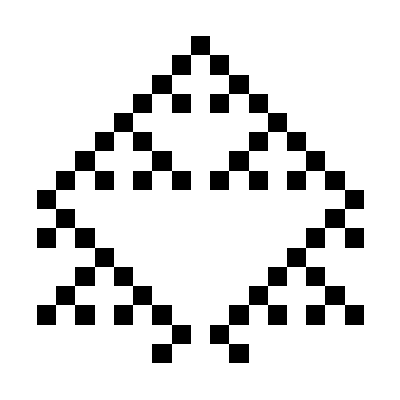

```mathematica
InitializeCPU[];
LoadProgram[machineCode];
RunProgram[22000]
```

```mathematica
ExecutionPlot[asm]
```

Positive:  | 0
Negative:  | 1
Zero:  | 0
NotZero:  | 1
Parity:  | 0ALU Status
Halted:  | TrueExecution status |  | Register A | Register B
Binary | 0000000001 | 0000010001
Decimal | 1 | 17
Instruction Register | Address Register
Opcode | Parameter
0000010000 | 0000000000
Return | 0 | Binary | 0111010110
Decimal | 470CU Status
Stack level | Binary value | Decimal value
1 | {0,0,0,0,0,0,0,0,0,0} | 0
2 | {0,0,0,0,0,0,0,0,0,0} | 0
3 | {0,0,0,0,0,0,0,0,0,0} | 0
4 | {0,0,0,0,0,0,0,0,0,0} | 0
5 | {0,0,0,0,0,0,0,0,0,0} | 0
6 | {0,0,0,0,0,0,0,0,0,0} | 0
7 | {0,0,0,0,0,0,0,0,0,0} | 0
8 | {0,0,0,0,0,0,0,0,0,0} | 0StackCPU-Graphics-Screen output | Text outputOutput
0 | SetA
1 | 0
2 | Store
3 | 771
4 | SetA
5 | 0
6 | Store
7 | 772
8 | SetA
9 | 0
10 | Store
11 | 773
12 | SetA
13 | 0
14 | Store
15 | 774
16 | SetA
17 | 0
18 | Store
19 | 775
20 | SetA
21 | 0
22 | Store
23 | 776
24 | SetA
25 | 0
26 | Store
27 | 777
28 | SetA
29 | 0
30 | Store
31 | 778
32 | SetA
33 | 1
34 | Store
35 | 779
36 | SetA
37 | 0
38 | Store
39 | 780
40 | SetA
41 | 0
42 | Store
43 | 781
44 | SetA
45 | 0
46 | Store
47 | 782
48 | SetA
49 | 0
50 | Store
51 | 783
52 | SetA
53 | 0
54 | Store
55 | 784
56 | SetA
57 | 0
58 | Store
59 | 785
60 | SetA
61 | 0
62 | Store
63 | 786 | 64 | SetA
65 | 0
66 | Store
67 | 787
68 | SetA
69 | 0
70 | Store
71 | 809
72 | SetA
73 | 16
74 | LoadB
75 | 809
76 | Substract
77 | 0
78 | JumpNeg
79 | 470
80 | Call
81 | 699
82 | SetA
83 | 0
84 | Store
85 | 805
86 | LoadA
87 | 771
88 | Store
89 | 806
90 | LoadA
91 | 772
92 | Store
93 | 807
94 | Call
95 | 473
96 | LoadA
97 | 808
98 | Store
99 | 788
100 | LoadA
101 | 771
102 | Store
103 | 805
104 | LoadA
105 | 772
106 | Store
107 | 806
108 | LoadA
109 | 773
110 | Store
111 | 807
112 | Call
113 | 473
114 | LoadA
115 | 808
116 | Store
117 | 789
118 | LoadA
119 | 772
120 | Store
121 | 805
122 | LoadA
123 | 773
124 | Store
125 | 806
126 | LoadA
127 | 774 | 128 | Store
129 | 807
130 | Call
131 | 473
132 | LoadA
133 | 808
134 | Store
135 | 790
136 | LoadA
137 | 773
138 | Store
139 | 805
140 | LoadA
141 | 774
142 | Store
143 | 806
144 | LoadA
145 | 775
146 | Store
147 | 807
148 | Call
149 | 473
150 | LoadA
151 | 808
152 | Store
153 | 791
154 | LoadA
155 | 774
156 | Store
157 | 805
158 | LoadA
159 | 775
160 | Store
161 | 806
162 | LoadA
163 | 776
164 | Store
165 | 807
166 | Call
167 | 473
168 | LoadA
169 | 808
170 | Store
171 | 792
172 | LoadA
173 | 775
174 | Store
175 | 805
176 | LoadA
177 | 776
178 | Store
179 | 806
180 | LoadA
181 | 777
182 | Store
183 | 807
184 | Call
185 | 473
186 | LoadA
187 | 808
188 | Store
189 | 793
190 | LoadA
191 | 776 | 192 | Store
193 | 805
194 | LoadA
195 | 777
196 | Store
197 | 806
198 | LoadA
199 | 778
200 | Store
201 | 807
202 | Call
203 | 473
204 | LoadA
205 | 808
206 | Store
207 | 794
208 | LoadA
209 | 777
210 | Store
211 | 805
212 | LoadA
213 | 778
214 | Store
215 | 806
216 | LoadA
217 | 779
218 | Store
219 | 807
220 | Call
221 | 473
222 | LoadA
223 | 808
224 | Store
225 | 795
226 | LoadA
227 | 778
228 | Store
229 | 805
230 | LoadA
231 | 779
232 | Store
233 | 806
234 | LoadA
235 | 780
236 | Store
237 | 807
238 | Call
239 | 473
240 | LoadA
241 | 808
242 | Store
243 | 796
244 | LoadA
245 | 779
246 | Store
247 | 805
248 | LoadA
249 | 780
250 | Store
251 | 806
252 | LoadA
253 | 781
254 | Store
255 | 807 | 256 | Call
257 | 473
258 | LoadA
259 | 808
260 | Store
261 | 797
262 | LoadA
263 | 780
264 | Store
265 | 805
266 | LoadA
267 | 781
268 | Store
269 | 806
270 | LoadA
271 | 782
272 | Store
273 | 807
274 | Call
275 | 473
276 | LoadA
277 | 808
278 | Store
279 | 798
280 | LoadA
281 | 781
282 | Store
283 | 805
284 | LoadA
285 | 782
286 | Store
287 | 806
288 | LoadA
289 | 783
290 | Store
291 | 807
292 | Call
293 | 473
294 | LoadA
295 | 808
296 | Store
297 | 799
298 | LoadA
299 | 782
300 | Store
301 | 805
302 | LoadA
303 | 783
304 | Store
305 | 806
306 | LoadA
307 | 784
308 | Store
309 | 807
310 | Call
311 | 473
312 | LoadA
313 | 808
314 | Store
315 | 800
316 | LoadA
317 | 783
318 | Store
319 | 805 | 320 | LoadA
321 | 784
322 | Store
323 | 806
324 | LoadA
325 | 785
326 | Store
327 | 807
328 | Call
329 | 473
330 | LoadA
331 | 808
332 | Store
333 | 801
334 | LoadA
335 | 784
336 | Store
337 | 805
338 | LoadA
339 | 785
340 | Store
341 | 806
342 | LoadA
343 | 786
344 | Store
345 | 807
346 | Call
347 | 473
348 | LoadA
349 | 808
350 | Store
351 | 802
352 | LoadA
353 | 785
354 | Store
355 | 805
356 | LoadA
357 | 786
358 | Store
359 | 806
360 | LoadA
361 | 787
362 | Store
363 | 807
364 | Call
365 | 473
366 | LoadA
367 | 808
368 | Store
369 | 803
370 | LoadA
371 | 786
372 | Store
373 | 805
374 | LoadA
375 | 787
376 | Store
377 | 806
378 | SetA
379 | 0
380 | Store
381 | 807
382 | Call
383 | 473 | 384 | LoadA
385 | 808
386 | Store
387 | 804
388 | LoadA
389 | 788
390 | Store
391 | 771
392 | LoadA
393 | 789
394 | Store
395 | 772
396 | LoadA
397 | 790
398 | Store
399 | 773
400 | LoadA
401 | 791
402 | Store
403 | 774
404 | LoadA
405 | 792
406 | Store
407 | 775
408 | LoadA
409 | 793
410 | Store
411 | 776
412 | LoadA
413 | 794
414 | Store
415 | 777
416 | LoadA
417 | 795
418 | Store
419 | 778
420 | LoadA
421 | 796
422 | Store
423 | 779
424 | LoadA
425 | 797
426 | Store
427 | 780
428 | LoadA
429 | 798
430 | Store
431 | 781
432 | LoadA
433 | 799
434 | Store
435 | 782
436 | LoadA
437 | 800
438 | Store
439 | 783
440 | LoadA
441 | 801
442 | Store
443 | 784
444 | LoadA
445 | 802
446 | Store
447 | 785 | 448 | LoadA
449 | 803
450 | Store
451 | 786
452 | LoadA
453 | 804
454 | Store
455 | 787
456 | LoadA
457 | 809
458 | SetB
459 | 1
460 | Add
461 | 0
462 | Store
463 | 472
464 | LoadA
465 | 472
466 | Store
467 | 809
468 | Jump
469 | 72
470 | Return
471 | 0
472 | 0
473 | SetA
474 | 1
475 | LoadB
476 | 805
477 | Substract
478 | 0
479 | JumpNotZero
480 | 501
481 | SetA
482 | 1
483 | LoadB
484 | 806
485 | Substract
486 | 0
487 | JumpNotZero
488 | 501
489 | SetA
490 | 1
491 | LoadB
492 | 807
493 | Substract
494 | 0
495 | JumpNotZero
496 | 501
497 | SetA
498 | 0
499 | Store
500 | 808
501 | SetA
502 | 1
503 | LoadB
504 | 805
505 | Substract
506 | 0
507 | JumpNotZero
508 | 529
509 | SetA
510 | 1
511 | LoadB | 512 | 806
513 | Substract
514 | 0
515 | JumpNotZero
516 | 529
517 | SetA
518 | 0
519 | LoadB
520 | 807
521 | Substract
522 | 0
523 | JumpNotZero
524 | 529
525 | SetA
526 | 1
527 | Store
528 | 808
529 | SetA
530 | 1
531 | LoadB
532 | 805
533 | Substract
534 | 0
535 | JumpNotZero
536 | 557
537 | SetA
538 | 0
539 | LoadB
540 | 806
541 | Substract
542 | 0
543 | JumpNotZero
544 | 557
545 | SetA
546 | 1
547 | LoadB
548 | 807
549 | Substract
550 | 0
551 | JumpNotZero
552 | 557
553 | SetA
554 | 0
555 | Store
556 | 808
557 | SetA
558 | 1
559 | LoadB
560 | 805
561 | Substract
562 | 0
563 | JumpNotZero
564 | 585
565 | SetA
566 | 0
567 | LoadB
568 | 806
569 | Substract
570 | 0
571 | JumpNotZero
572 | 585
573 | SetA
574 | 0
575 | LoadB | 576 | 807
577 | Substract
578 | 0
579 | JumpNotZero
580 | 585
581 | SetA
582 | 1
583 | Store
584 | 808
585 | SetA
586 | 0
587 | LoadB
588 | 805
589 | Substract
590 | 0
591 | JumpNotZero
592 | 613
593 | SetA
594 | 1
595 | LoadB
596 | 806
597 | Substract
598 | 0
599 | JumpNotZero
600 | 613
601 | SetA
602 | 1
603 | LoadB
604 | 807
605 | Substract
606 | 0
607 | JumpNotZero
608 | 613
609 | SetA
610 | 1
611 | Store
612 | 808
613 | SetA
614 | 0
615 | LoadB
616 | 805
617 | Substract
618 | 0
619 | JumpNotZero
620 | 641
621 | SetA
622 | 1
623 | LoadB
624 | 806
625 | Substract
626 | 0
627 | JumpNotZero
628 | 641
629 | SetA
630 | 0
631 | LoadB
632 | 807
633 | Substract
634 | 0
635 | JumpNotZero
636 | 641
637 | SetA
638 | 0
639 | Store | 640 | 808
641 | SetA
642 | 0
643 | LoadB
644 | 805
645 | Substract
646 | 0
647 | JumpNotZero
648 | 669
649 | SetA
650 | 0
651 | LoadB
652 | 806
653 | Substract
654 | 0
655 | JumpNotZero
656 | 669
657 | SetA
658 | 1
659 | LoadB
660 | 807
661 | Substract
662 | 0
663 | JumpNotZero
664 | 669
665 | SetA
666 | 1
667 | Store
668 | 808
669 | SetA
670 | 0
671 | LoadB
672 | 805
673 | Substract
674 | 0
675 | JumpNotZero
676 | 697
677 | SetA
678 | 0
679 | LoadB
680 | 806
681 | Substract
682 | 0
683 | JumpNotZero
684 | 697
685 | SetA
686 | 0
687 | LoadB
688 | 807
689 | Substract
690 | 0
691 | JumpNotZero
692 | 697
693 | SetA
694 | 0
695 | Store
696 | 808
697 | Return
698 | 0
699 | LoadA
700 | 809
701 | SetB
702 | 0
703 | Draw | 704 | 771
705 | SetB
706 | 1
707 | Draw
708 | 772
709 | SetB
710 | 2
711 | Draw
712 | 773
713 | SetB
714 | 3
715 | Draw
716 | 774
717 | SetB
718 | 4
719 | Draw
720 | 775
721 | SetB
722 | 5
723 | Draw
724 | 776
725 | SetB
726 | 6
727 | Draw
728 | 777
729 | SetB
730 | 7
731 | Draw
732 | 778
733 | SetB
734 | 8
735 | Draw
736 | 779
737 | SetB
738 | 9
739 | Draw
740 | 780
741 | SetB
742 | 10
743 | Draw
744 | 781
745 | SetB
746 | 11
747 | Draw
748 | 782
749 | SetB
750 | 12
751 | Draw
752 | 783
753 | SetB
754 | 13
755 | Draw
756 | 784
757 | SetB
758 | 14
759 | Draw
760 | 785
761 | SetB
762 | 15
763 | Draw
764 | 786
765 | SetB
766 | 16
767 | Draw | 768 | 787
769 | Return
770 | 0
771 | 0
772 | 0
773 | 0
774 | 0
775 | 0
776 | 0
777 | 0
778 | 0
779 | 0
780 | 0
781 | 0
782 | 0
783 | 0
784 | 0
785 | 0
786 | 0
787 | 0
788 | 0
789 | 0
790 | 0
791 | 0
792 | 0
793 | 0
794 | 0
795 | 0
796 | 0
797 | 0
798 | 0
799 | 0
800 | 0
801 | 0
802 | 0
803 | 0
804 | 0
805 | 0
806 | 0
807 | 0
808 | 0
809 | 0ProgramMemory